```mathematica
ϕ[x_,y_,λ1_,λ2_]:=2(x+y)-(2 λ1+λ2)(Cos[x]+Cos[y])+λ2 Cos[x] Cos[y]
```

```mathematica
diagphi[x_,λ1_, λ2_]:=ϕ[x,x,λ1,λ2]
```

```mathematica
Manipulate[Plot[diagphi[x,λ1,λ2],{x,-Pi,Pi}],{λ1,0,10},{λ2,0,10}]
```

```mathematica
Solve[{D[diagphi[x,λ1,λ2],x]==0,D[diagphi[x,λ1,λ2],{x,2}]>0,-Pi<=x<Pi,λ1>=0,λ2>=0 },x]
```

{{x→ConditionalExpression[2 ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]], ]}}

{{x→ConditionalExpression[2 ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]], ]}}

{{x→ConditionalExpression[2 ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]], ]}}

«2 more identical outputs»

{{x→ConditionalExpression[2 ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]], (ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]]∈ℝ&&λ2≥0&&λ1>1)||(ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]]∈ℝ&&0<λ1≤1&&λ2>Root[-16 λ1^4+16 λ1^6+(-32 λ1^3+48 λ1^5) #1+(-64+56 λ1^2+48 λ1^4) #1^2+(72 λ1+16 λ1^3) #1^3+27 #1^4&,2])]}}

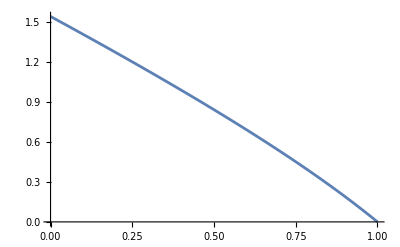

```mathematica
Plot[Root[-16 λ1^4+16 λ1^6+(-32 λ1^3+48 λ1^5) #1+(-64+56 λ1^2+48 λ1^4) #1^2+(72 λ1+16 λ1^3) #1^3+27 #1^4&,2],{λ1,0,1}]
```

```mathematica
H[x_,y_,λ1_,λ2_]:=ResourceFunction["HessianMatrix"][ϕ[x,y,λ1,λ2],{x,y}]
```

```mathematica
e1[x_,y_,λ1_,λ2_]:=Eigenvalues[H[x,y,λ1,λ2]][[1]]
```

```mathematica
e2[x_,y_,λ1_,λ2_]:=Eigenvalues[H[x,y,λ1,λ2]][[2]]
e1[x,y,λ1,λ2]
```

1/4 (4 λ1 Cos[x]+2 λ2 Cos[x]-2 λ2 Cos[x-y]+4 λ1 Cos[y]+2 λ2 Cos[y]-2 λ2 Cos[x+y]-√2 √(8 λ1^2+8 λ1 λ2+4 λ2^2+4 λ1^2 Cos[2 x]+4 λ1 λ2 Cos[2 x]-λ2^2 Cos[2 x]+λ2^2 Cos[2 x-2 y]-8 λ1^2 Cos[x-y]-8 λ1 λ2 Cos[x-y]-2 λ2^2 Cos[x-y]+4 λ1^2 Cos[2 y]+4 λ1 λ2 Cos[2 y]-λ2^2 Cos[2 y]-8 λ1^2 Cos[x+y]-8 λ1 λ2 Cos[x+y]-2 λ2^2 Cos[x+y]+λ2^2 Cos[2 x+2 y]))

```mathematica
e2[x,y,λ1,λ2]
```

1/4 (4 λ1 Cos[x]+2 λ2 Cos[x]-2 λ2 Cos[x-y]+4 λ1 Cos[y]+2 λ2 Cos[y]-2 λ2 Cos[x+y]+√2 √(8 λ1^2+8 λ1 λ2+4 λ2^2+4 λ1^2 Cos[2 x]+4 λ1 λ2 Cos[2 x]-λ2^2 Cos[2 x]+λ2^2 Cos[2 x-2 y]-8 λ1^2 Cos[x-y]-8 λ1 λ2 Cos[x-y]-2 λ2^2 Cos[x-y]+4 λ1^2 Cos[2 y]+4 λ1 λ2 Cos[2 y]-λ2^2 Cos[2 y]-8 λ1^2 Cos[x+y]-8 λ1 λ2 Cos[x+y]-2 λ2^2 Cos[x+y]+λ2^2 Cos[2 x+2 y]))

```mathematica
eigenva2[x_,y_,λ1_,λ2_]:=1/4 (4 λ1 Cos[x]+2 λ2 Cos[x]-2 λ2 Cos[x-y]+4 λ1 Cos[y]+2 λ2 Cos[y]-2 λ2 Cos[x+y]+√2 √(8 λ1^2+8 λ1 λ2+4 λ2^2+4 λ1^2 Cos[2 x]+4 λ1 λ2 Cos[2 x]-λ2^2 Cos[2 x]+λ2^2 Cos[2 x-2 y]-8 λ1^2 Cos[x-y]-8 λ1 λ2 Cos[x-y]-2 λ2^2 Cos[x-y]+4 λ1^2 Cos[2 y]+4 λ1 λ2 Cos[2 y]-λ2^2 Cos[2 y]-8 λ1^2 Cos[x+y]-8 λ1 λ2 Cos[x+y]-2 λ2^2 Cos[x+y]+λ2^2 Cos[2 x+2 y]))
```

```mathematica
eigenva1[x_,y_,λ1_,λ2_]:=1/4 (4 λ1 Cos[x]+2 λ2 Cos[x]-2 λ2 Cos[x-y]+4 λ1 Cos[y]+2 λ2 Cos[y]-2 λ2 Cos[x+y]-√2 √(8 λ1^2+8 λ1 λ2+4 λ2^2+4 λ1^2 Cos[2 x]+4 λ1 λ2 Cos[2 x]-λ2^2 Cos[2 x]+λ2^2 Cos[2 x-2 y]-8 λ1^2 Cos[x-y]-8 λ1 λ2 Cos[x-y]-2 λ2^2 Cos[x-y]+4 λ1^2 Cos[2 y]+4 λ1 λ2 Cos[2 y]-λ2^2 Cos[2 y]-8 λ1^2 Cos[x+y]-8 λ1 λ2 Cos[x+y]-2 λ2^2 Cos[x+y]+λ2^2 Cos[2 x+2 y]))
```

```mathematica
e1stationary[λ1_,λ2_]:=eigenva1[2 ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]],2 ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]],λ1,λ2]
```

```mathematica
e2stationary[λ1_,λ2_]:=eigenva2[2 ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]],2 ArcTan[Root[1+2 λ1 #1+2 #1^2+(2 λ1+2 λ2) #1^3+#1^4&,2]],λ1,λ2]
```

```mathematica
Reduce[{e1stationary[λ1,λ2]>0, e2stationary[λ1,λ2]>0,λ1>0,λ2>0},{λ1,λ2}]
```

$Aborted

```mathematica
dat=Table[{λ1,Root[-16 λ1^4+16 λ1^6+(-32 λ1^3+48 λ1^5) #1+(-64+56 λ1^2+48 λ1^4) #1^2+(72 λ1+16 λ1^3) #1^3+27 #1^4&,2]},{λ1,0,1,.001}]
```

{{0.,0.},{0.001,1.53827},{0.002,1.53693},{0.003,1.5356},{0.004,1.53427},{0.005,1.53293},{0.006,1.5316},{0.007,1.53026},{0.008,1.52893},{0.009,1.52759},{0.01,1.52626},{0.011,1.52492},{0.012,1.52359},{0.013,1.52225},{0.014,1.52092},{0.015,1.51958},{0.016,1.51824},{0.017,1.51691},{0.018,1.51557},{0.019,1.51423},{0.02,1.5129},{0.021,1.51156},{0.022,1.51022},{0.023,1.50888},{0.024,1.50754},{0.025,1.50621},{0.026,1.50487},{0.027,1.50353},{0.028,1.50219},{0.029,1.50085},{0.03,1.49951},{0.031,1.49817},{0.032,1.49683},{0.033,1.49549},{0.034,1.49415},{0.035,1.49281},{0.036,1.49147},{0.037,1.49013},{0.038,1.48879},{0.039,1.48745},{0.04,1.48611},{0.041,1.48477},{0.042,1.48343},{0.043,1.48209},{0.044,1.48074},{0.045,1.4794},{0.046,1.47806},{0.047,1.47672},{0.048,1.47537},{0.049,1.47403},{0.05,1.47269},{0.051,1.47134},{0.052,1.47},{0.053,1.46866},{0.054,1.46731},{0.055,1.46597},{0.056,1.46462},{0.057,1.46328},{0.058,1.46193},{0.059,1.46059},{0.06,1.45924},{0.061,1.4579},{0.062,1.45655},{0.063,1.45521},{0.064,1.45386},{0.065,1.45251},{0.066,1.45117},{0.067,1.44982},{0.068,1.44847},{0.069,1.44713},{0.07,1.44578},{0.071,1.44443},{0.072,1.44308},{0.073,1.44174},{0.074,1.44039},{0.075,1.43904},{0.076,1.43769},{0.077,1.43634},{0.078,1.43499},{0.079,1.43364},{0.08,1.43229},{0.081,1.43094},{0.082,1.42959},{0.083,1.42824},{0.084,1.42689},{0.085,1.42554},{0.086,1.42419},{0.087,1.42284},{0.088,1.42149},{0.089,1.42014},{0.09,1.41879},{0.091,1.41743},{0.092,1.41608},{0.093,1.41473},{0.094,1.41338},{0.095,1.41202},{0.096,1.41067},{0.097,1.40932},{0.098,1.40796},{0.099,1.40661},{0.1,1.40526},{0.101,1.4039},{0.102,1.40255},{0.103,1.40119},{0.104,1.39984},{0.105,1.39848},{0.106,1.39713},{0.107,1.39577},{0.108,1.39442},{0.109,1.39306},{0.11,1.3917},{0.111,1.39035},{0.112,1.38899},{0.113,1.38763},{0.114,1.38628},{0.115,1.38492},{0.116,1.38356},{0.117,1.3822},{0.118,1.38085},{0.119,1.37949},{0.12,1.37813},{0.121,1.37677},{0.122,1.37541},{0.123,1.37405},{0.124,1.37269},{0.125,1.37133},{0.126,1.36997},{0.127,1.36861},{0.128,1.36725},{0.129,1.36589},{0.13,1.36453},{0.131,1.36317},{0.132,1.36181},{0.133,1.36045},{0.134,1.35909},{0.135,1.35772},{0.136,1.35636},{0.137,1.355},{0.138,1.35364},{0.139,1.35227},{0.14,1.35091},{0.141,1.34955},{0.142,1.34818},{0.143,1.34682},{0.144,1.34545},{0.145,1.34409},{0.146,1.34273},{0.147,1.34136},{0.148,1.34},{0.149,1.33863},{0.15,1.33726},{0.151,1.3359},{0.152,1.33453},{0.153,1.33317},{0.154,1.3318},{0.155,1.33043},{0.156,1.32907},{0.157,1.3277},{0.158,1.32633},{0.159,1.32496},{0.16,1.3236},{0.161,1.32223},{0.162,1.32086},{0.163,1.31949},{0.164,1.31812},{0.165,1.31675},{0.166,1.31538},{0.167,1.31401},{0.168,1.31264},{0.169,1.31127},{0.17,1.3099},{0.171,1.30853},{0.172,1.30716},{0.173,1.30579},{0.174,1.30442},{0.175,1.30305},{0.176,1.30167},{0.177,1.3003},{0.178,1.29893},{0.179,1.29756},{0.18,1.29618},{0.181,1.29481},{0.182,1.29344},{0.183,1.29206},{0.184,1.29069},{0.185,1.28931},{0.186,1.28794},{0.187,1.28656},{0.188,1.28519},{0.189,1.28381},{0.19,1.28244},{0.191,1.28106},{0.192,1.27969},{0.193,1.27831},{0.194,1.27693},{0.195,1.27556},{0.196,1.27418},{0.197,1.2728},{0.198,1.27142},{0.199,1.27005},{0.2,1.26867},{0.201,1.26729},{0.202,1.26591},{0.203,1.26453},{0.204,1.26315},{0.205,1.26177},{0.206,1.26039},{0.207,1.25901},{0.208,1.25763},{0.209,1.25625},{0.21,1.25487},{0.211,1.25349},{0.212,1.25211},{0.213,1.25073},{0.214,1.24934},{0.215,1.24796},{0.216,1.24658},{0.217,1.2452},{0.218,1.24381},{0.219,1.24243},{0.22,1.24105},{0.221,1.23966},{0.222,1.23828},{0.223,1.23689},{0.224,1.23551},{0.225,1.23412},{0.226,1.23274},{0.227,1.23135},{0.228,1.22997},{0.229,1.22858},{0.23,1.2272},{0.231,1.22581},{0.232,1.22442},{0.233,1.22304},{0.234,1.22165},{0.235,1.22026},{0.236,1.21887},{0.237,1.21748},{0.238,1.2161},{0.239,1.21471},{0.24,1.21332},{0.241,1.21193},{0.242,1.21054},{0.243,1.20915},{0.244,1.20776},{0.245,1.20637},{0.246,1.20498},{0.247,1.20359},{0.248,1.20219},{0.249,1.2008},{0.25,1.19941},{0.251,1.19802},{0.252,1.19663},{0.253,1.19523},{0.254,1.19384},{0.255,1.19245},{0.256,1.19105},{0.257,1.18966},{0.258,1.18826},{0.259,1.18687},{0.26,1.18547},{0.261,1.18408},{0.262,1.18268},{0.263,1.18129},{0.264,1.17989},{0.265,1.1785},{0.266,1.1771},{0.267,1.1757},{0.268,1.1743},{0.269,1.17291},{0.27,1.17151},{0.271,1.17011},{0.272,1.16871},{0.273,1.16731},{0.274,1.16591},{0.275,1.16452},{0.276,1.16312},{0.277,1.16172},{0.278,1.16032},{0.279,1.15892},{0.28,1.15751},{0.281,1.15611},{0.282,1.15471},{0.283,1.15331},{0.284,1.15191},{0.285,1.15051},{0.286,1.1491},{0.287,1.1477},{0.288,1.1463},{0.289,1.14489},{0.29,1.14349},{0.291,1.14208},{0.292,1.14068},{0.293,1.13928},{0.294,1.13787},{0.295,1.13646},{0.296,1.13506},{0.297,1.13365},{0.298,1.13225},{0.299,1.13084},{0.3,1.12943},{0.301,1.12803},{0.302,1.12662},{0.303,1.12521},{0.304,1.1238},{0.305,1.12239},{0.306,1.12098},{0.307,1.11957},{0.308,1.11817},{0.309,1.11676},{0.31,1.11535},{0.311,1.11393},{0.312,1.11252},{0.313,1.11111},{0.314,1.1097},{0.315,1.10829},{0.316,1.10688},{0.317,1.10546},{0.318,1.10405},{0.319,1.10264},{0.32,1.10123},{0.321,1.09981},{0.322,1.0984},{0.323,1.09698},{0.324,1.09557},{0.325,1.09415},{0.326,1.09274},{0.327,1.09132},{0.328,1.08991},{0.329,1.08849},{0.33,1.08707},{0.331,1.08566},{0.332,1.08424},{0.333,1.08282},{0.334,1.0814},{0.335,1.07998},{0.336,1.07856},{0.337,1.07715},{0.338,1.07573},{0.339,1.07431},{0.34,1.07289},{0.341,1.07147},{0.342,1.07004},{0.343,1.06862},{0.344,1.0672},{0.345,1.06578},{0.346,1.06436},{0.347,1.06294},{0.348,1.06151},{0.349,1.06009},{0.35,1.05867},{0.351,1.05724},{0.352,1.05582},{0.353,1.05439},{0.354,1.05297},{0.355,1.05154},{0.356,1.05012},{0.357,1.04869},{0.358,1.04726},{0.359,1.04584},{0.36,1.04441},{0.361,1.04298},{0.362,1.04156},{0.363,1.04013},{0.364,1.0387},{0.365,1.03727},{0.366,1.03584},{0.367,1.03441},{0.368,1.03298},{0.369,1.03155},{0.37,1.03012},{0.371,1.02869},{0.372,1.02726},{0.373,1.02583},{0.374,1.02439},{0.375,1.02296},{0.376,1.02153},{0.377,1.0201},{0.378,1.01866},{0.379,1.01723},{0.38,1.01579},{0.381,1.01436},{0.382,1.01292},{0.383,1.01149},{0.384,1.01005},{0.385,1.00862},{0.386,1.00718},{0.387,1.00574},{0.388,1.00431},{0.389,1.00287},{0.39,1.00143},{0.391,0.999992},{0.392,0.998553},{0.393,0.997114},{0.394,0.995675},{0.395,0.994235},{0.396,0.992794},{0.397,0.991354},{0.398,0.989913},{0.399,0.988471},{0.4,0.987029},{0.401,0.985587},{0.402,0.984145},{0.403,0.982702},{0.404,0.981258},{0.405,0.979815},{0.406,0.97837},{0.407,0.976926},{0.408,0.975481},{0.409,0.974036},{0.41,0.97259},{0.411,0.971144},{0.412,0.969697},{0.413,0.96825},{0.414,0.966803},{0.415,0.965355},{0.416,0.963907},{0.417,0.962459},{0.418,0.96101},{0.419,0.959561},{0.42,0.958111},{0.421,0.956661},{0.422,0.95521},{0.423,0.95376},{0.424,0.952308},{0.425,0.950857},{0.426,0.949404},{0.427,0.947952},{0.428,0.946499},{0.429,0.945046},{0.43,0.943592},{0.431,0.942138},{0.432,0.940683},{0.433,0.939228},{0.434,0.937773},{0.435,0.936317},{0.436,0.934861},{0.437,0.933404},{0.438,0.931947},{0.439,0.93049},{0.44,0.929032},{0.441,0.927574},{0.442,0.926115},{0.443,0.924656},{0.444,0.923196},{0.445,0.921736},{0.446,0.920276},{0.447,0.918815},{0.448,0.917354},{0.449,0.915892},{0.45,0.91443},{0.451,0.912968},{0.452,0.911505},{0.453,0.910041},{0.454,0.908577},{0.455,0.907113},{0.456,0.905649},{0.457,0.904183},{0.458,0.902718},{0.459,0.901252},{0.46,0.899785},{0.461,0.898319},{0.462,0.896851},{0.463,0.895384},{0.464,0.893915},{0.465,0.892447},{0.466,0.890978},{0.467,0.889508},{0.468,0.888038},{0.469,0.886568},{0.47,0.885097},{0.471,0.883626},{0.472,0.882154},{0.473,0.880682},{0.474,0.879209},{0.475,0.877736},{0.476,0.876263},{0.477,0.874789},{0.478,0.873314},{0.479,0.871839},{0.48,0.870364},{0.481,0.868888},{0.482,0.867412},{0.483,0.865935},{0.484,0.864458},{0.485,0.86298},{0.486,0.861502},{0.487,0.860024},{0.488,0.858544},{0.489,0.857065},{0.49,0.855585},{0.491,0.854105},{0.492,0.852624},{0.493,0.851142},{0.494,0.84966},{0.495,0.848178},{0.496,0.846695},{0.497,0.845212},{0.498,0.843728},{0.499,0.842244},{0.5,0.840759},{0.501,0.839274},{0.502,0.837788},{0.503,0.836302},{0.504,0.834816},{0.505,0.833329},{0.506,0.831841},{0.507,0.830353},{0.508,0.828864},{0.509,0.827375},{0.51,0.825886},{0.511,0.824396},{0.512,0.822905},{0.513,0.821414},{0.514,0.819923},{0.515,0.818431},{0.516,0.816938},{0.517,0.815445},{0.518,0.813952},{0.519,0.812458},{0.52,0.810963},{0.521,0.809468},{0.522,0.807973},{0.523,0.806477},{0.524,0.80498},{0.525,0.803483},{0.526,0.801985},{0.527,0.800487},{0.528,0.798989},{0.529,0.79749},{0.53,0.79599},{0.531,0.79449},{0.532,0.79299},{0.533,0.791488},{0.534,0.789987},{0.535,0.788485},{0.536,0.786982},{0.537,0.785479},{0.538,0.783975},{0.539,0.782471},{0.54,0.780966},{0.541,0.779461},{0.542,0.777955},{0.543,0.776449},{0.544,0.774942},{0.545,0.773434},{0.546,0.771926},{0.547,0.770418},{0.548,0.768909},{0.549,0.767399},{0.55,0.765889},{0.551,0.764379},{0.552,0.762867},{0.553,0.761356},{0.554,0.759843},{0.555,0.758331},{0.556,0.756817},{0.557,0.755303},{0.558,0.753789},{0.559,0.752274},{0.56,0.750758},{0.561,0.749242},{0.562,0.747726},{0.563,0.746208},{0.564,0.744691},{0.565,0.743172},{0.566,0.741654},{0.567,0.740134},{0.568,0.738614},{0.569,0.737094},{0.57,0.735572},{0.571,0.734051},{0.572,0.732528},{0.573,0.731006},{0.574,0.729482},{0.575,0.727958},{0.576,0.726434},{0.577,0.724909},{0.578,0.723383},{0.579,0.721857},{0.58,0.72033},{0.581,0.718802},{0.582,0.717274},{0.583,0.715746},{0.584,0.714216},{0.585,0.712687},{0.586,0.711156},{0.587,0.709625},{0.588,0.708094},{0.589,0.706562},{0.59,0.705029},{0.591,0.703496},{0.592,0.701962},{0.593,0.700427},{0.594,0.698892},{0.595,0.697356},{0.596,0.69582},{0.597,0.694283},{0.598,0.692746},{0.599,0.691207},{0.6,0.689669},{0.601,0.688129},{0.602,0.686589},{0.603,0.685049},{0.604,0.683508},{0.605,0.681966},{0.606,0.680423},{0.607,0.67888},{0.608,0.677337},{0.609,0.675792},{0.61,0.674247},{0.611,0.672702},{0.612,0.671156},{0.613,0.669609},{0.614,0.668061},{0.615,0.666513},{0.616,0.664964},{0.617,0.663415},{0.618,0.661865},{0.619,0.660314},{0.62,0.658763},{0.621,0.657211},{0.622,0.655659},{0.623,0.654105},{0.624,0.652552},{0.625,0.650997},{0.626,0.649442},{0.627,0.647886},{0.628,0.64633},{0.629,0.644773},{0.63,0.643215},{0.631,0.641656},{0.632,0.640097},{0.633,0.638537},{0.634,0.636977},{0.635,0.635416},{0.636,0.633854},{0.637,0.632292},{0.638,0.630728},{0.639,0.629165},{0.64,0.6276},{0.641,0.626035},{0.642,0.624469},{0.643,0.622903},{0.644,0.621336},{0.645,0.619768},{0.646,0.618199},{0.647,0.61663},{0.648,0.61506},{0.649,0.613489},{0.65,0.611918},{0.651,0.610346},{0.652,0.608773},{0.653,0.6072},{0.654,0.605626},{0.655,0.604051},{0.656,0.602475},{0.657,0.600899},{0.658,0.599322},{0.659,0.597744},{0.66,0.596166},{0.661,0.594587},{0.662,0.593007},{0.663,0.591426},{0.664,0.589845},{0.665,0.588263},{0.666,0.58668},{0.667,0.585097},{0.668,0.583513},{0.669,0.581928},{0.67,0.580342},{0.671,0.578756},{0.672,0.577169},{0.673,0.575581},{0.674,0.573992},{0.675,0.572403},{0.676,0.570813},{0.677,0.569222},{0.678,0.56763},{0.679,0.566038},{0.68,0.564445},{0.681,0.562851},{0.682,0.561256},{0.683,0.559661},{0.684,0.558065},{0.685,0.556468},{0.686,0.55487},{0.687,0.553272},{0.688,0.551673},{0.689,0.550073},{0.69,0.548472},{0.691,0.546871},{0.692,0.545268},{0.693,0.543665},{0.694,0.542061},{0.695,0.540457},{0.696,0.538851},{0.697,0.537245},{0.698,0.535638},{0.699,0.53403},{0.7,0.532421},{0.701,0.530812},{0.702,0.529202},{0.703,0.527591},{0.704,0.525979},{0.705,0.524366},{0.706,0.522753},{0.707,0.521138},{0.708,0.519523},{0.709,0.517907},{0.71,0.516291},{0.711,0.514673},{0.712,0.513055},{0.713,0.511436},{0.714,0.509816},{0.715,0.508195},{0.716,0.506573},{0.717,0.50495},{0.718,0.503327},{0.719,0.501703},{0.72,0.500078},{0.721,0.498452},{0.722,0.496825},{0.723,0.495197},{0.724,0.493569},{0.725,0.49194},{0.726,0.490309},{0.727,0.488678},{0.728,0.487046},{0.729,0.485414},{0.73,0.48378},{0.731,0.482146},{0.732,0.48051},{0.733,0.478874},{0.734,0.477237},{0.735,0.475599},{0.736,0.47396},{0.737,0.47232},{0.738,0.470679},{0.739,0.469038},{0.74,0.467395},{0.741,0.465752},{0.742,0.464108},{0.743,0.462462},{0.744,0.460816},{0.745,0.459169},{0.746,0.457521},{0.747,0.455873},{0.748,0.454223},{0.749,0.452572},{0.75,0.450921},{0.751,0.449268},{0.752,0.447615},{0.753,0.44596},{0.754,0.444305},{0.755,0.442649},{0.756,0.440992},{0.757,0.439333},{0.758,0.437674},{0.759,0.436014},{0.76,0.434354},{0.761,0.432692},{0.762,0.431029},{0.763,0.429365},{0.764,0.4277},{0.765,0.426034},{0.766,0.424368},{0.767,0.4227},{0.768,0.421031},{0.769,0.419362},{0.77,0.417691},{0.771,0.41602},{0.772,0.414347},{0.773,0.412674},{0.774,0.410999},{0.775,0.409323},{0.776,0.407647},{0.777,0.405969},{0.778,0.404291},{0.779,0.402611},{0.78,0.400931},{0.781,0.399249},{0.782,0.397567},{0.783,0.395883},{0.784,0.394199},{0.785,0.392513},{0.786,0.390826},{0.787,0.389139},{0.788,0.38745},{0.789,0.38576},{0.79,0.384069},{0.791,0.382378},{0.792,0.380685},{0.793,0.378991},{0.794,0.377296},{0.795,0.3756},{0.796,0.373903},{0.797,0.372205},{0.798,0.370505},{0.799,0.368805},{0.8,0.367104},{0.801,0.365401},{0.802,0.363698},{0.803,0.361993},{0.804,0.360288},{0.805,0.358581},{0.806,0.356873},{0.807,0.355164},{0.808,0.353454},{0.809,0.351743},{0.81,0.350031},{0.811,0.348317},{0.812,0.346603},{0.813,0.344887},{0.814,0.343171},{0.815,0.341453},{0.816,0.339734},{0.817,0.338014},{0.818,0.336293},{0.819,0.33457},{0.82,0.332847},{0.821,0.331122},{0.822,0.329396},{0.823,0.327669},{0.824,0.325941},{0.825,0.324212},{0.826,0.322482},{0.827,0.32075},{0.828,0.319018},{0.829,0.317284},{0.83,0.315549},{0.831,0.313812},{0.832,0.312075},{0.833,0.310336},{0.834,0.308597},{0.835,0.306856},{0.836,0.305114},{0.837,0.30337},{0.838,0.301626},{0.839,0.29988},{0.84,0.298133},{0.841,0.296385},{0.842,0.294635},{0.843,0.292885},{0.844,0.291133},{0.845,0.28938},{0.846,0.287625},{0.847,0.28587},{0.848,0.284113},{0.849,0.282355},{0.85,0.280595},{0.851,0.278835},{0.852,0.277073},{0.853,0.27531},{0.854,0.273546},{0.855,0.27178},{0.856,0.270013},{0.857,0.268245},{0.858,0.266475},{0.859,0.264705},{0.86,0.262933},{0.861,0.261159},{0.862,0.259385},{0.863,0.257609},{0.864,0.255832},{0.865,0.254053},{0.866,0.252273},{0.867,0.250492},{0.868,0.24871},{0.869,0.246926},{0.87,0.245141},{0.871,0.243354},{0.872,0.241566},{0.873,0.239777},{0.874,0.237987},{0.875,0.236195},{0.876,0.234401},{0.877,0.232607},{0.878,0.230811},{0.879,0.229014},{0.88,0.227215},{0.881,0.225415},{0.882,0.223613},{0.883,0.221811},{0.884,0.220006},{0.885,0.218201},{0.886,0.216394},{0.887,0.214585},{0.888,0.212775},{0.889,0.210964},{0.89,0.209152},{0.891,0.207337},{0.892,0.205522},{0.893,0.203705},{0.894,0.201887},{0.895,0.200067},{0.896,0.198246},{0.897,0.196423},{0.898,0.194599},{0.899,0.192773},{0.9,0.190946},{0.901,0.189117},{0.902,0.187287},{0.903,0.185456},{0.904,0.183623},{0.905,0.181789},{0.906,0.179953},{0.907,0.178115},{0.908,0.176276},{0.909,0.174436},{0.91,0.172594},{0.911,0.17075},{0.912,0.168905},{0.913,0.167059},{0.914,0.165211},{0.915,0.163361},{0.916,0.16151},{0.917,0.159657},{0.918,0.157803},{0.919,0.155947},{0.92,0.15409},{0.921,0.152231},{0.922,0.150371},{0.923,0.148509},{0.924,0.146645},{0.925,0.14478},{0.926,0.142913},{0.927,0.141045},{0.928,0.139175},{0.929,0.137303},{0.93,0.13543},{0.931,0.133556},{0.932,0.131679},{0.933,0.129801},{0.934,0.127921},{0.935,0.12604},{0.936,0.124157},{0.937,0.122273},{0.938,0.120387},{0.939,0.118499},{0.94,0.116609},{0.941,0.114718},{0.942,0.112825},{0.943,0.110931},{0.944,0.109034},{0.945,0.107137},{0.946,0.105237},{0.947,0.103336},{0.948,0.101433},{0.949,0.0995281},{0.95,0.0976217},{0.951,0.0957136},{0.952,0.0938038},{0.953,0.0918923},{0.954,0.089979},{0.955,0.088064},{0.956,0.0861472},{0.957,0.0842287},{0.958,0.0823085},{0.959,0.0803865},{0.96,0.0784627},{0.961,0.0765371},{0.962,0.0746098},{0.963,0.0726807},{0.964,0.0707498},{0.965,0.0688171},{0.966,0.0668826},{0.967,0.0649463},{0.968,0.0630082},{0.969,0.0610683},{0.97,0.0591266},{0.971,0.057183},{0.972,0.0552376},{0.973,0.0532904},{0.974,0.0513413},{0.975,0.0493904},{0.976,0.0474377},{0.977,0.045483},{0.978,0.0435265},{0.979,0.0415682},{0.98,0.0396079},{0.981,0.0376458},{0.982,0.0356818},{0.983,0.0337159},{0.984,0.0317481},{0.985,0.0297783},{0.986,0.0278067},{0.987,0.0258332},{0.988,0.0238577},{0.989,0.0218803},{0.99,0.019901},{0.991,0.0179197},{0.992,0.0159365},{0.993,0.0139513},{0.994,0.0119642},{0.995,0.00997512},{0.996,0.00798406},{0.997,0.00599103},{0.998,0.00399601},{0.999,0.001999},{1.,0.}}

```mathematica
Export["Uni/Msc-unitn/Thesis/Zeno/quantum-zeni/data/dimer-stages-I-II-analytical.dat",dat]
```

Uni/Msc-unitn/Thesis/Zeno/quantum-zeni/data/dimer-stages-I-II-analytical.dat